```mathematica
a=2+4
```

6

```mathematica
a
```

6

```mathematica
b=pippo
```

pippo

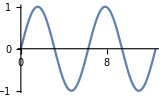

```mathematica
Plot[Sin[x], {x,0,4 Pi}]
```

```mathematica
b
```

pippo

```mathematica
Head[pippo]
```

Symbol

```mathematica
Head[5]
```

Integer

```mathematica
Head[5.]
```

Real

```mathematica
Head["pippo"]
```

String

```mathematica
??*Plot*
```

```mathematica
Series[ Sin[z], {z,0,5}]
```

z-z^3/6+z^5/120+O[z]^6

```mathematica
Integrate[ a x^2 + b x + c, {x,xmin,xmax}] (* esempio di integrale definito *)
```

c (xmax-xmin)+pippo (xmax^2/2-xmin^2/2)+6 (xmax^3/3-xmin^3/3)

```mathematica
Head[ %4 ]
```

Graphics

```mathematica
Series[ f[x], {x,x0,3}]
```

f[x0]+f'[x0] (x-x0)+1/2 f''[x0] (x-x0)^2+1/6 f^(3)[x0] (x-x0)^3+O[x-x0]^4

```mathematica
FullForm[ %21 ]
```

SeriesData[x,x0,List[f[x0],Derivative[1][f][x0],Times[Rational[1,2],Derivative[2][f][x0]],Times[Rational[1,6],Derivative[3][f][x0]]],0,4,1]

```mathematica
FullForm[ 1 + 2 x + x^2 ]
```

Plus[1,Times[2,x],Power[x,2]]

```mathematica
FullForm[ (1+x)^2 ]
```

Power[Plus[1,x],2]

```mathematica
lista={"z",pippo,99}
```

{z,pippo,99}

```mathematica
lista[[0]]
```

List

```mathematica
expr=(r+s)(x+y)(w+z)
```

(r+s) (x+y) (w+z)

```mathematica
expr[[3,0]]
```

Plus

```mathematica
expr /. {z->pluto}
```

(r+s) (pluto+w) (x+y)

```mathematica
expr
```

(r+s) (x+y) (w+z)

```mathematica
Clear[a,b]
```

```mathematica
Solve[ a x + b == 0, a]
```

{{a→-b/x}}

```mathematica
sol=Solve[ a x^2 + b x + c == 0, x ]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
x /. sol
```

{(-b-√(b^2-4 a c))/(2 a),(-b+√(b^2-4 a c))/(2 a)}

```mathematica
sol2 = Solve[ {a x + b y == k1, c x + d y == k2}, {x,y}]
```

{{x→-(d k1-b k2)/(b c-a d),y→-(-c k1+a k2)/(b c-a d)}}

```mathematica
M={ {a,b},{c,d} }
```

{{a,b},{c,d}}

```mathematica
inc = {x,y}
```

{x,y}

```mathematica
known = {k1,k2}
```

{k1,k2}

```mathematica
Solve[ M.inc == known, inc]
```

{{x→-(d k1-b k2)/(b c-a d),y→-(-c k1+a k2)/(b c-a d)}}

```mathematica
M.inc
```

{a x+b y,c x+d y}

```mathematica
inc.M
```

{a x+c y,b x+d y}

```mathematica
inc.known
```

k1 x+k2 y

```mathematica
inc known
```

{k1 x,k2 y}

```mathematica
5 inc
```

{5 x,5 y}

```mathematica
2/7
```

2/7

```mathematica
N[2/7., 32]
```

0.285714

```mathematica
N[2/7, 32]
```

0.28571428571428571428571428571429

```mathematica
Sin[Pi/4.]
```

0.707107

```mathematica
Log[3 - I Pi]
```

Log[3-ⅈ π]

```mathematica
Log[3.-I Pi]
```

1.46878-0.808449 ⅈ

```mathematica
Log[-1]
```

ⅈ π

```mathematica
f[x_] := a x^2 + b x + c
```

```mathematica
f[4]
```

16 a+4 b+c

```mathematica
f[pippo]
```

c+b pippo+a pippo^2

```mathematica
f["pippo"]
```

pippo^2 a+pippo b+c

```mathematica
f[x]=pluto
```

pluto

```mathematica
f[a]
```

a^3+a b+c

```mathematica
f[y]
```

c+b y+a y^2

```mathematica
f[x]
```

pluto

```mathematica
g[x_,y_] = a x^2 + b y^2
```

a x^2+b y^2

```mathematica
Log[0.1]
```

-2.30259

```mathematica
serie[n_] = Normal[ Series[ Log[1+x], {x,0,n}] ]
```

Series::serlim: Series order specification n is not a machine-sized integer.

Log[1+x]

```mathematica
serie /. x->-0.9
```

serie

```mathematica
Clear[serie]
```

```mathematica
Do[ 
numerico = serie[n]/.x->-0.9;
errore = Abs[ numerico/Log[0.1] -1];
Print[n,"  ",errore],
{n,1,100}]
```

1  Abs[-1-0.434294 serie[1]]

2  Abs[-1-0.434294 serie[2]]

3  Abs[-1-0.434294 serie[3]]

4  Abs[-1-0.434294 serie[4]]

5  Abs[-1-0.434294 serie[5]]

6  Abs[-1-0.434294 serie[6]]

7  Abs[-1-0.434294 serie[7]]

8  Abs[-1-0.434294 serie[8]]

9  Abs[-1-0.434294 serie[9]]

10  Abs[-1-0.434294 serie[10]]

11  Abs[-1-0.434294 serie[11]]

12  Abs[-1-0.434294 serie[12]]

13  Abs[-1-0.434294 serie[13]]

14  Abs[-1-0.434294 serie[14]]

15  Abs[-1-0.434294 serie[15]]

16  Abs[-1-0.434294 serie[16]]

17  Abs[-1-0.434294 serie[17]]

18  Abs[-1-0.434294 serie[18]]

19  Abs[-1-0.434294 serie[19]]

20  Abs[-1-0.434294 serie[20]]

21  Abs[-1-0.434294 serie[21]]

22  Abs[-1-0.434294 serie[22]]

23  Abs[-1-0.434294 serie[23]]

24  Abs[-1-0.434294 serie[24]]

25  Abs[-1-0.434294 serie[25]]

26  Abs[-1-0.434294 serie[26]]

27  Abs[-1-0.434294 serie[27]]

28  Abs[-1-0.434294 serie[28]]

29  Abs[-1-0.434294 serie[29]]

30  Abs[-1-0.434294 serie[30]]

31  Abs[-1-0.434294 serie[31]]

32  Abs[-1-0.434294 serie[32]]

33  Abs[-1-0.434294 serie[33]]

34  Abs[-1-0.434294 serie[34]]

35  Abs[-1-0.434294 serie[35]]

36  Abs[-1-0.434294 serie[36]]

37  Abs[-1-0.434294 serie[37]]

38  Abs[-1-0.434294 serie[38]]

39  Abs[-1-0.434294 serie[39]]

40  Abs[-1-0.434294 serie[40]]

41  Abs[-1-0.434294 serie[41]]

42  Abs[-1-0.434294 serie[42]]

43  Abs[-1-0.434294 serie[43]]

44  Abs[-1-0.434294 serie[44]]

45  Abs[-1-0.434294 serie[45]]

46  Abs[-1-0.434294 serie[46]]

47  Abs[-1-0.434294 serie[47]]

48  Abs[-1-0.434294 serie[48]]

49  Abs[-1-0.434294 serie[49]]

50  Abs[-1-0.434294 serie[50]]

51  Abs[-1-0.434294 serie[51]]

52  Abs[-1-0.434294 serie[52]]

53  Abs[-1-0.434294 serie[53]]

54  Abs[-1-0.434294 serie[54]]

55  Abs[-1-0.434294 serie[55]]

56  Abs[-1-0.434294 serie[56]]

57  Abs[-1-0.434294 serie[57]]

58  Abs[-1-0.434294 serie[58]]

59  Abs[-1-0.434294 serie[59]]

60  Abs[-1-0.434294 serie[60]]

61  Abs[-1-0.434294 serie[61]]

62  Abs[-1-0.434294 serie[62]]

63  Abs[-1-0.434294 serie[63]]

64  Abs[-1-0.434294 serie[64]]

65  Abs[-1-0.434294 serie[65]]

66  Abs[-1-0.434294 serie[66]]

67  Abs[-1-0.434294 serie[67]]

68  Abs[-1-0.434294 serie[68]]

69  Abs[-1-0.434294 serie[69]]

70  Abs[-1-0.434294 serie[70]]

71  Abs[-1-0.434294 serie[71]]

72  Abs[-1-0.434294 serie[72]]

73  Abs[-1-0.434294 serie[73]]

74  Abs[-1-0.434294 serie[74]]

75  Abs[-1-0.434294 serie[75]]

76  Abs[-1-0.434294 serie[76]]

77  Abs[-1-0.434294 serie[77]]

78  Abs[-1-0.434294 serie[78]]

79  Abs[-1-0.434294 serie[79]]

80  Abs[-1-0.434294 serie[80]]

81  Abs[-1-0.434294 serie[81]]

82  Abs[-1-0.434294 serie[82]]

83  Abs[-1-0.434294 serie[83]]

84  Abs[-1-0.434294 serie[84]]

85  Abs[-1-0.434294 serie[85]]

86  Abs[-1-0.434294 serie[86]]

87  Abs[-1-0.434294 serie[87]]

88  Abs[-1-0.434294 serie[88]]

89  Abs[-1-0.434294 serie[89]]

90  Abs[-1-0.434294 serie[90]]

91  Abs[-1-0.434294 serie[91]]

92  Abs[-1-0.434294 serie[92]]

93  Abs[-1-0.434294 serie[93]]

94  Abs[-1-0.434294 serie[94]]

95  Abs[-1-0.434294 serie[95]]

96  Abs[-1-0.434294 serie[96]]

97  Abs[-1-0.434294 serie[97]]

98  Abs[-1-0.434294 serie[98]]

99  Abs[-1-0.434294 serie[99]]

100  Abs[-1-0.434294 serie[100]]